# 实验数据集成处理平台

## 中国科学技术大学 化学物理系 禤科材 PB20030874 Wolfram Mathematica 13.0.1.0，平台版本：1.0.0

### 创建脚本

```mathematica
#!Plus[a,b]
```

自动创建脚本https://www.wolfram.com/mathematica/new-in-8/mathematica-shell-scripts/mathematica--script-from-your-code.html

## 大学物理-基础实验A

## 一维：均值与不确定度

### 样本数据处理

#### 数据输入

```mathematica
Clear["Global`*"]
Tdistribution={0,12.71,4.30,3.18,2.78,2.57,2.45,2.36,2.31,2.26,2.23,2.20,2.18,2.16,2.14,2.13,2.12,2.11,2.10,2.09,2.09,1.96};(*这是t分布需要乘的参数列表*)

data1=Import["/Users/royalty/Documents/A gift for your 20th birthday/数据处理平台/sample data1.txt","List"]   (*从文件中读取数据，注意文件中数据的摆放形式：同组数据以空格间断、以回车符为一组数据的分割*)

(*或者也可以手动输入数据：data={1.1,1.12,1.04,1.23,1.09,1.15,1.07,1.16,1.02},不过有点麻烦*)

(*到你的电脑上之后文件的路径会发生变化，输入Import[""]的""时候会自动弹出"文件浏览器"的按钮，点击即可找到要导入的文件*)

(*Export[]的使用方法和Import[]差不多，参见帮助文档*)
```

{1.1,1.12,1.04,1.23,1.09,1.15,1.07,1.16,1.02}

#### 不确定度计算

样本平均值:1.10889

样本标准差:0.0648931

A类不确定度:0.0499677

B类不确定度:0.0461976

展伸不确定度（P=0.95）:0.0680514

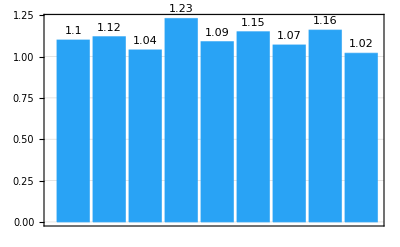

```mathematica
number=Length[data1];(*数组长度*)
average=Mean[data1]//N;(*平均值*)
st=StandardDeviation[data1]//N;(*data的标准差*)

(*A类不确定度*)
If[
number>21,
UA=Tdistribution[[22]]*st/Sqrt[number],
UA=Tdistribution[[number]]*st/Sqrt[number];
]

(*B类不确定度*)
gudu=0.05;        (*估读误差*)
yiqi=0.05;       (*仪器误差*)
zhixin=3;         (*置信系数*)
UB=1.96*(√(gudu^2+yiqi^2))/zhixin;

(*总不确定度*)
U=√(UA^2+UB^2);

(*输出*)
Print["样本平均值:",average]
Print["样本标准差:",st]
Print["A类不确定度:",UA]
Print["B类不确定度:",UB]
Print["展伸不确定度（P=0.95）:",U]
BarChart[data1,PlotRange->Full,PlotTheme->"Detailed",ChartLabels->Placed[data1,Above],
ChartStyle->RGBColor[0.16, 0.64, 0.96]
]
```

```mathematica
RandomColor[]
```

RGBColor[0.09798006958105376, 0.4145480748221486, 0.05306167632890646]

### 剔除异常

{1.1,1.12,1.04,1.23,1.09,1.15,1.07,1.16,1.02}

第 4 组数据 1.23 和平均值有最大相对偏差 10.9218%

剔除后平均值:1.09375

剔除后标准差:0.0495516. 相对之前变化：-0.0153415

剔除后A类不确定度:0.0381547. 相对之前变化：-0.011813

剔除后B类不确定度:0.0461976

剔除后展伸不确定度（P=0.95）:0.0599166. 相对之前变化：-0.00813474

-Graphics-

{1.1,1.12,1.04,1.09,1.15,1.07,1.16,1.02}

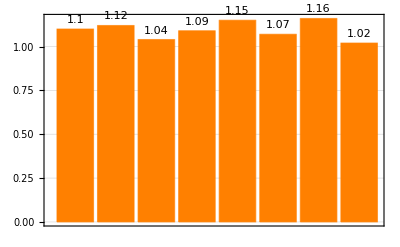

```mathematica
difference=Abs[data1-average];
data1
For[i=1,i<=number, i++,
If[difference[[i]]==Max[difference],
Print["第 ",i," 组数据 ",data1[[i]]," 和平均值有最大相对偏差 ",Max[difference]/average*100,"%"];
aim=i;
Break;
]]     (*for循环，寻找离平均值最远的点*)

t=0;
If[aim==1,newdata1=data1[[2;;number]];t=1;]
If[aim==number,newdata1=data1[[1;;number-1]];t=1;]
If[t!=1,forward=data1[[1;;aim-1]];back=data1[[aim+1;;number]];newdata1=Join[forward,back];]    (*剔除编号为aim的数据*)

newnumber=Length[newdata1];(*平均值*)
average=Mean[newdata1]//N;
newst=StandardDeviation[newdata1]//N;(*newdata的标准差*)
If[
newnumber>21,
newUA=Tdistribution[[22]]*newst/Sqrt[number],
newUA=Tdistribution[[number]]*newst/Sqrt[number];
](*A类不确定度*)

gudu=0.05;       (*估读误差*)
yiqi=0.05;      (*仪器误差*)
zhixin=3; (*置信系数*)
UB=1.96*(√(gudu^2+yiqi^2))/zhixin;(*B类不确定度*)

newU=√(newUA^2+UB^2);(*总不确定度*)

Print["剔除后平均值:",average]
Print["剔除后标准差:",newst,". 相对之前变化：",newst-st]
Print["剔除后A类不确定度:",newUA,". 相对之前变化：",newUA-UA]
Print["剔除后B类不确定度:",UB]
Print["剔除后展伸不确定度（P=0.95）:",newU, ". 相对之前变化：",newU-U]
BarChart[data1,PlotRange->Full,PlotTheme->"Detailed",ChartLabels->Placed[data1,Above],
ChartStyle->RGBColor[0.16, 0.64, 0.96]]

t=0;
t=Input["是否从测量序列中剔除此数（样本容量需要足够大）？确认请填1："];
If[t==1,data1=newdata1;number=newnumber;data1,data1]
BarChart[data1,PlotRange->Full,PlotTheme->"Detailed",ChartLabels->Placed[data1,Above],
ChartStyle->Orange]
```

```mathematica
Clear["Global`*"](*清除符号变量占有的内存*)
```

## 二维：拟合与不确定度

### 线性回归与残差

#### 散点图

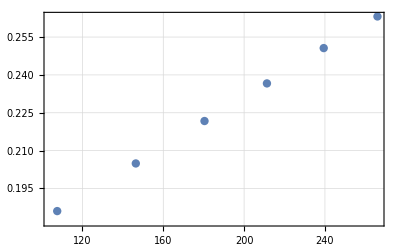

```mathematica
Clear["Global`*"]
Tdistribution={0,12.71,4.30,3.18,2.78,2.57,2.45,2.36,2.31,2.26,2.23,2.20,2.18,2.16,2.14,2.13,2.12,2.11,2.10,2.09,2.09,1.96};(*这是t分布需要乘的参数列表*)
data2=Import["/Users/royalty/Documents/A gift for your 20th birthday/数据处理平台/sample data2.txt","Table"];(*注意，这里是以"Table"(表格)格式导入二维数据，前面一维数据的导入只需要"List"(列表)*)
ListPlot[data2,PlotTheme->"Detailed",PlotStyle->Directive[PointSize->0.015]]
number=Length[data2];
```

#### 线性回归模型

FittedModel[0.000487716 x+0.133625]

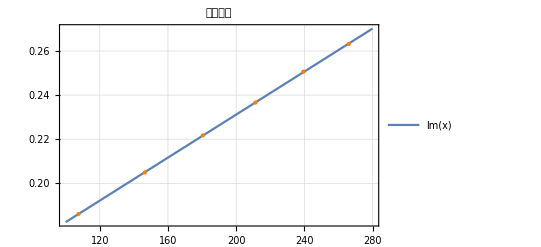

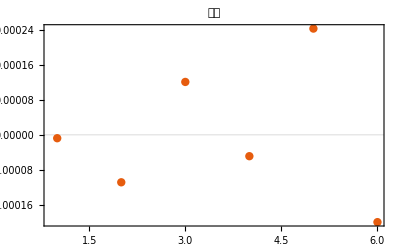

```mathematica
lm=LinearModelFit[data2,x,x];
TraditionalForm[lm]
Show[Plot[lm[x],{x,100,280},PlotLabel->HoldForm[线性回归],PlotTheme->"Detailed"],ListPlot[data2,PlotStyle->Directive[Orange,PointSize->0.015],PlotTheme->"Detailed"]]
ListPlot[lm["FitResiduals"],Frame->True,PlotRange->All,PlotLabel->HoldForm[残差],PlotStyle->Directive[PointSize->0.015],PlotTheme->"Scientific"]
```

#### 不确定度计算

```mathematica
R=-lm["CorrelationMatrix"][[1,2]];
b=lm["BestFitParameters"][[1]];
k=lm["BestFitParameters"][[2]];
Print["相关系数:",R]
Print["截距:",b]
Print["斜率:",k]

Print["各点横坐标:", Table[data2[[i,1]],{i,1,number}]]
Print["横坐标平方平均值：",average=Total[Table[data2[[i,1]]^2,{i,1,number}]]/number]
s1=k*√((1/R-1)/(number-2));
s2=√average*s1;
If[number-2>20,
u2=s2*Tdistribution[[22]];
u1=s1*Tdistribution[[22]],

u2=s2*Tdistribution[[number-2]];
  u1=s1*Tdistribution[[number-2]];
]
Print["斜率标准差:",s1]
Print["截距标准差:",s2]
Print["斜率展伸不确定度:",u1]
Print["截距展伸不确定度:",u2]
```

相关系数:0.962684

截距:0.133625

斜率:0.000487716

各点横坐标:{107.5,146.4,180.4,211.3,239.4,266}

横坐标平方平均值：39708.2

斜率标准差:0.0000480112

截距标准差:0.00956715

斜率展伸不确定度:0.000152676

截距展伸不确定度:0.0304235

### 自定义函数的回归分析

#### 散点图

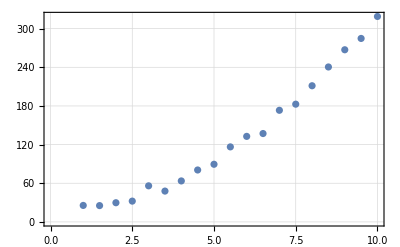

```mathematica
Tdistribution={0,12.71,4.30,3.18,2.78,2.57,2.45,2.36,2.31,2.26,2.23,2.20,2.18,2.16,2.14,2.13,2.12,2.11,2.10,2.09,2.09,1.96};(*这是t分布需要乘的参数列表*)
data=Table[{i,3i^2+20+RandomReal[{-10,10}]},{i,1,10,0.5}];(*这是一些以3x^2+20为中心波
动的随机数列，只是示例*)
ListPlot[data,PlotTheme->"Detailed"]
```

#### 建立回归模型

{x}↦3.02305 x^2-0.167443 x+19.1976

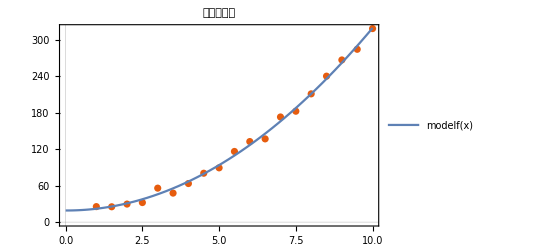

```mathematica
Clear[a,b,c]
model=a x^2+b x+c;
fit=FindFit[data,model,{a,b,c},x];
modelf=Function[{x},Evaluate[model/.fit]];
TraditionalForm[modelf]
Show[ListPlot[data,PlotLabel->HoldForm[非线性回归],PlotTheme->"Scientific"],Plot[modelf[x],{x,0,10},PlotTheme->"Detailed"]]
```

```mathematica
FindFormula[data](*MATHEMATICA内置函数，直接找到一组数据的最佳拟合，可能会与其他方法得到的结果有出入*)
```

17.3506+3.01904 #1^2.&

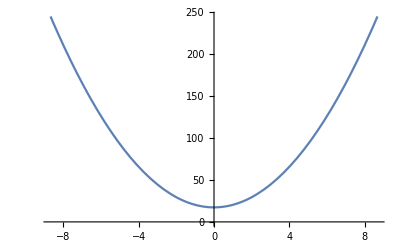

```mathematica
Plot[(17.35059866445689+3.019036910826073 #1^2.&)[x],{x,-8.687687999154425,8.687687999154425}]
```

## 物理化学基础实验（上）

### 初始化

```mathematica
experimentnumber=6;

(*实验编号,与文件夹编号相同，比如一号实验文件夹的名称为exp1，二号实验文件夹名称为exp2，否则后面的文件导入导出会有报错*)

path="/Users/royalty/Desktop/Experiments_for_Chemistry/physical_chemistry";
SetDirectory[path]

(*请注意，mac系统路径使用的是/，而 windows系统路径是\*)

<<draw.wl
<<file.wl
<<fitting.wl

(*读入 Wolfram 个人函数包，它们应当已经被放在了"/Users/royalty/Desktop/Experiments_for_Chemistry/physical_chemistry"里面*)
```

/Users/royalty/Desktop/Experiments_for_Chemistry/physical_chemistry

```mathematica
?Draw`*
```

```mathematica
?DataFile`*
```

```mathematica
?Fitting`*
```

### 数据文件基础

#### 数据的导入

```mathematica
data=ImportDataFile[path,experimentnumber];
data//Length
filenumber=Length[data];

(*可能需要剔除一些没有导入成功的数据，输出文件的长度以检查*)
```

9

```mathematica
data=Drop[data,-1];
filenumber=Length[data]

(*由于ImportFiles 函数使用 For 循环导入名称已经标准化的.txt文件，文件个数包含了系统隐藏的文件，所以此处需要手动去除这些未导入成功的文件*)
```

8

#### 基础绘图

```mathematica
legends=LegendsName[path,experimentnumber]

(*可能需要调整一下图例的顺序，和导入文件的顺序可能不同*)
```

{{125 - DTC - 冷却水},{125 - DTC},{125 - 继电器 - 冷却水},{125 - 继电器},{200 - DTC - 冷却水},{200 - DTC},{200 - 继电器 - 冷却水},{200 - 继电器}}

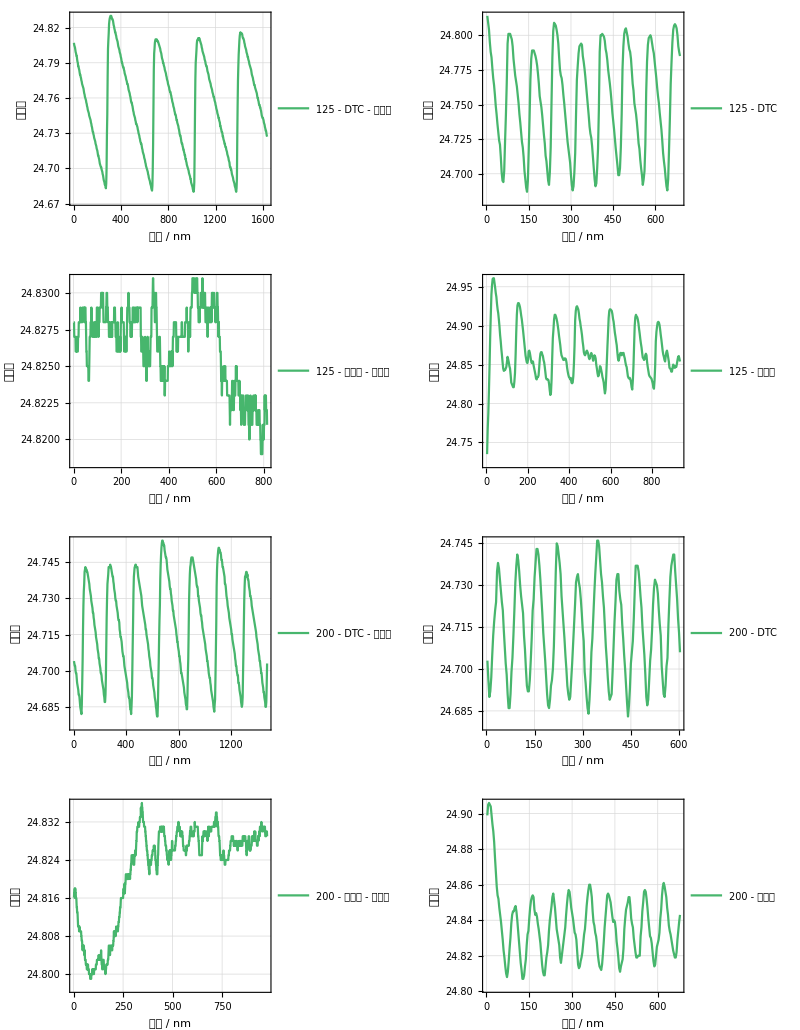

```mathematica
(*legends={{"组别1"},{"组别2"},{"组别3"},{"组别4"},{"组别5"},{"组别6"},{"组别7"},{"极碱"},{"极酸"},{"基线"}};*)

(*图例内容*)

place= Table[{0.87, 0.9},{i,1,filenumber}];
(*place={{0.92, 0.9},{0.92, 0.9},{0.92, 0.9},{0.92, 0.9},{0.92, 0.9},{0.92, 0.9},{0.92, 0.9},{0.92, 0.9},{0.92, 0.9},{0.92, 0.9}};*)

(*图例位置*)

framelabel=Table[{"波长 / nm","吸光度"},{i,1,filenumber}];

(*{{"波长 / nm","吸光度"},{"波长 / nm","吸光度"},{"波长 / nm","吸光度"},{"波长 / nm","吸光度"},{"波长 / nm","吸光度"},{"波长 / nm","吸光度"},{"波长 / nm","吸光度"},{"波长 / nm","吸光度"},{"波长 / nm","吸光度"},{"波长 / nm","吸光度"}};*)

(*轴标签如果相同可以一次性设置，可以分别设置*)

plotrange=Table[All,{i,1,filenumber}];

(*plotrange={{-0.1,0.8},{-0.1,0.8},{-0.1,0.8},{-0.1,0.8},{-0.1,0.8},{-0.1,0.8},{-0.1,0.8},{-0.1,0.8},{-0.1,0.8},{-0.1,0.8}};*)

(*图例、位置以及边框标签的设置直接放在这里，如果对输出的图片不满意可以随时改动*)

images=PlotAll[data,legends,place,framelabel,97,plotrange];
plotassenble=GraphicsGrid[Partition[images,2],ImageSize->Full]
```

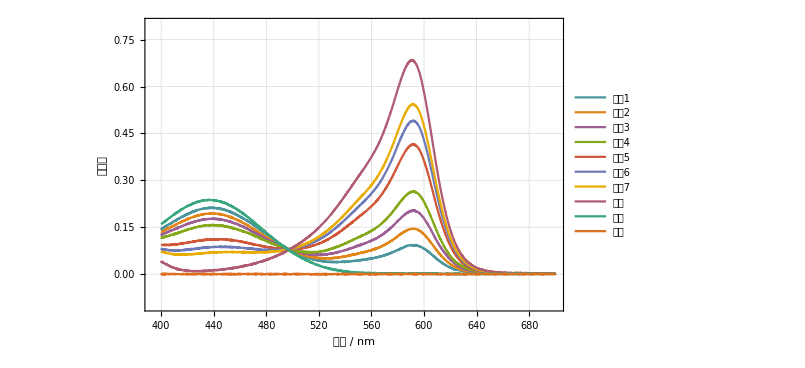

```mathematica
PlotInOne[data,legends,{0.87,0.6},framelabel[[1]],98,plotrange[[1]]]
```

```mathematica
plotwithdot[data_]:=Module[
	{j,x,withdot,l=Length[data]},
	withdot=Array[x,l];
	For[j=1,j<=l,j++,
		withdot[[j]]=
	]
]
```

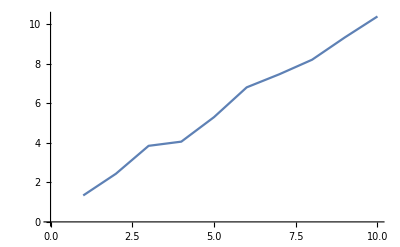

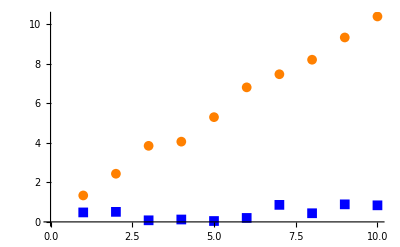

```mathematica
table1=Table[{i,i+RandomReal[]},{i,1,10}];
table2=Table[{i,RandomReal[]},{i,1,10}];
ListLinePlot[table1]
ListPlot[{table1,table2},PlotStyle->{Directive[Orange],Directive[Blue]},PlotMarkers->{Automatic,Medium}]
```

```mathematica
×
```

### 拟合数据并绘图

#### 数据的导入与变换

由于从仪器中得到的原始数据可能需要经过一些变换才能呈现线性形式，所以此处必须手动操作。

```mathematica
rawdata=ImportDataFitFile[path,experimentnumber];
rawdata//Length
(*导入原始数据，检查有无错误*)
```

2

```mathematica
rawdata=Drop[rawdata,-1]
```

{{{303.15,442.318},{308.15,437.51},{313.15,433.898},{318.15,429.885}}}

```mathematica
rawdata=rawdata//ToExpression;
(*转化为可计算的表达式*)    
datafit=Array[x,Length[rawdata]];datafit[[1]]=Table[rawdata[[1,i]],{i,Length[rawdata[[1]]]}];datafit[[2]]=Table[rawdata[[2,i]],{i,Length[rawdata[[2]]]}];datafit[[3]]=Table[rawdata[[3,i]],{i,Length[rawdata[[3]]]}];
datafit[[4]]=Table[rawdata[[4,i]],{i,Length[rawdata[[4]]]}];
(*根据实验的物理意义对横坐标纵坐标做相应变换，使其满足线性关系*)

ListPlot[datafit[[4]],PlotTheme->"Detailed",PlotRange->All]
(*检查数据点是否落在一条直线上*)
```

ListPlot[{{{303.15,442.318},{308.15,437.51},{313.15,433.898},{318.15,429.885}}}⟦4⟧,PlotTheme→Detailed,PlotRange→All]

```mathematica
ExportDataFitFile[path,experimentnumber,datafit]
(*新建fit_input文件夹，导出标准化名称的数据文件.txt，方便 SingleLinearFit 函数直接绘图*)
```

```mathematica
datafit
```

{{{303.15,442.318},{308.15,437.51},{313.15,433.898},{318.15,429.885}}}

#### 回归可视化

```mathematica
path
```

/Users/royalty/Desktop/Experiments_for_Chemistry/physical_chemistry

```mathematica
linearmodel=SingleLinearFit[path,experimentnumber,x]
```

{FittedModel[690.082-0.81822 x],LinearModelFit[$Failed,x,x]}

```mathematica
linearmodel=Drop[linearmodel,-1];
(*读入 fit_input 文件夹中名称已经标准化的数据文件.txt，求生成拟合模型*)
```

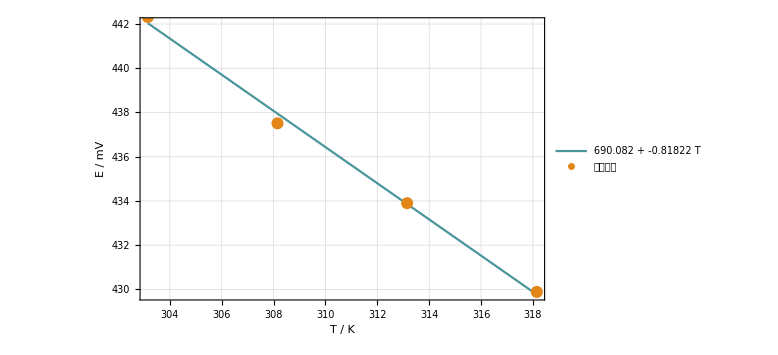

```mathematica
fitframelabel=Table[{"T / K","E / mV"},{i,1,Length[linearmodel]}];
(*fitframelabel={{"T / K","E / mV"}};*)
(*轴标签*)

fitlegends=ModelLegends[linearmodel,T];
(*从拟合模型中提取 BestFitParameters 以生成图例。需要输入形式自变量*)

dotlegends={{"电压均值"}};

fitplace=Table[{0.75,0.8},{i,1,Length[linearmodel]}] ;
(*fitplace= {{0.2, 0.85},{0.2, 0.85},{0.2, 0.85},{0.2, 0.85},{0.2, 0.85},{0.2, 0.85},{0.2, 0.85},{0.2, 0.85}};*)

legendsplace=Table[fitplace[[i]]+{-0.075,-0.1},{i,1,Length[fitplace]}];
(*图例位置*)

modelvisualized=PlotLinearFit[datafit,linearmodel,fitlegends,dotlegends,fitplace,legendsplace,fitframelabel,98];
Show[modelvisualized[[1,1]],modelvisualized[[1,2]]]

(*给出拟合直线、散点图、残差图、相关矩阵*)
```

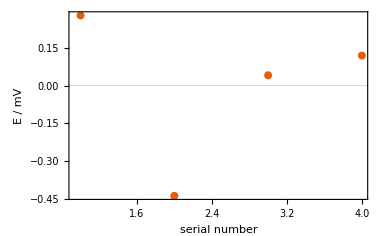

```mathematica
modelvisualized[[1,3]]
dots=ListPlot[datafit[[1]],PlotLegends -> Placed[LineLegend[dotlegends[[1]], LegendFunction -> Frame], legendsplace[[1]]],PlotStyle->Directive[Orange],PlotMarkers->{Automatic,Scaled[0.025]},PlotRange->All];
```

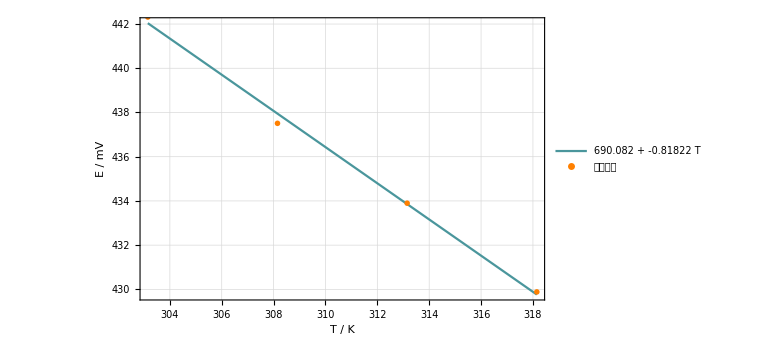

```mathematica
Show[modelvisualized[[1,1]],dots]
```

```mathematica
plotex=%
```

-Graphics-

#### 回归不确定度

```mathematica
modelnumber=1;
R=Abs[linearmodel[[modelnumber]]["CorrelationMatrix"][[1,2]]];
b=linearmodel[[modelnumber]]["BestFitParameters"][[1]];
k=linearmodel[[modelnumber]]["BestFitParameters"][[2]];
Print["相关系数:",R]
Print["截距:",b]
Print["斜率:",k]


Print["各点横坐标:", Table[data2[[i,1]],{i,1,number}]]
Print["横坐标平方平均值：",average=Total[Table[data2[[i,1]]^2,{i,1,number}]]/number]
s1=k*√((1/R-1)/(number-2));
s2=√average*s1;
If[number-2>20,
u2=s2*Tdistribution[[22]];
u1=s1*Tdistribution[[22]],

u2=s2*Tdistribution[[number-2]];
  u1=s1*Tdistribution[[number-2]];
]
Print["斜率标准差:",s1]
Print["截距标准差:",s2]
Print["斜率展伸不确定度:",u1]
Print["截距展伸不确定度:",u2]
```

相关系数:0.962684

截距:0.133625

斜率:0.000487716

各点横坐标:{107.5,146.4,180.4,211.3,239.4,266}

横坐标平方平均值：39708.2

斜率标准差:0.0000480112

截距标准差:0.00956715

斜率展伸不确定度:0.000152676

截距展伸不确定度:0.0304235

#### 误差

```mathematica
DeclarePackage["ErrorBarPlots`","ErrorListPlot"];
ErrorList
```

ErrorList

```mathematica
<<ErrorBarPlots`
```

```mathematica
ErrorListPlot
```

ErrorListPlot

#### 非线性回归

{x}↦-0.0000170927 x^2+0.0108609 x+1.1608

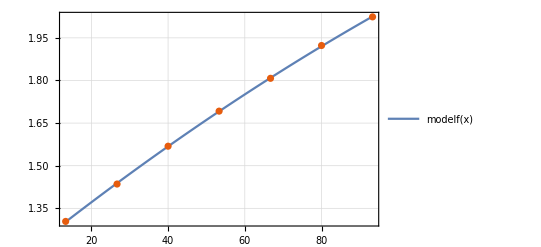

```mathematica
Clear[a,b,c]
model=a x^2+b x+c;
fit=FindFit[datafit,model,{a,b,c},x];
modelf=Function[{x},Evaluate[model/.fit]];
TraditionalForm[modelf]
Show[Plot[modelf[x],{x,datafit[[1,1]],datafit[[Length[datafit],1]]},PlotTheme->"Detailed"],ListPlot[datafit,PlotLabel->HoldForm[非线性回归],PlotTheme->"Scientific"]]
```

```mathematica
FindFormula[rawdata[[3]]]
```

0.567753+#1&

### TEX 交互

#### 图片导出

直接绘图，不拟合

```mathematica
ExportJpg[path,images,experimentnumber]
Export[path<>"/Kecai_Xuan/exp"<>ToString[experimentnumber]<>"/figure/Figure_all.jpg",plotassenble];
```

仅拟合

```mathematica
ExportJpg[path,{plotex},experimentnumber]
```

直接绘图 + 线性拟合

```mathematica
(*ExportJpg[path,images,experimentnumber]
Export[path<>"/Kecai_Xuan/exp1/Figure_all.jpg",plotassenble];*)
```

#### 图片引用

```mathematica
path
```

/Users/royalty/Desktop/Experiments_for_Chemistry/physical_chemistry

```mathematica
imgcode="\\"<>"begin{figure}[ht]\n"<>"\t\\"<>"centering\n"<>"\t\\"<>"includegraphics[width=___"<>"\\"<>"textwidth]{___}\n"<>"\t\\"<>"caption{___}\n"<>"\t\\"<>"label{fig:___}\n"<>"\\"<>"end{figure}\n"
```

```mathematica
figwidth={0.6,1,1,1,1,1,1,1};
figcaption={"电动势与温度的关系","ss","ss","ss","ss","ss","ss","ss"};
figlabel={"1","ss","ss","ss","ss","ss","ss","ss"};

ImageCode[path,experimentnumber,figwidth,figcaption,figlabel]//Column
```

\begin{figure}[ht]
	\centering
	\includegraphics[width=0.6\textwidth]{Figure_1.jpg}
	\caption{电动势与温度的关系}
	\label{fig:1}
\end{figure}

```mathematica
{{"\\begin{figure}[ht]\\n\\t\\centering\\n\\includegraphics[width=0.6\\textwidth]{Figure_1.jpg}\\n\\t\\caption{电动势与温度的关系}\\n\\t\\label{fig:1}\\n\\end{figure}\\n"}}
```

\begin{figure}[ht]
	\centering
	\includegraphics[width=1\textwidth]{Figure_1.jpg}
	\caption{ss}
	\label{fig:ss}
\end{figure}

#### 表格

```mathematica
table=Table[i+j,{i,1,10},{j,0,10}];
```

```mathematica
textablecode=TableCode[table]
```

```mathematica
Directory[]
```

/Users/royalty/Desktop/Experiments_for_Chemistry/physical_chemistry